```mathematica
s[n_]:=Module[{mat},
mat=ConstantArray[0,{n,n}];
For[i=1,i≤n,i++,
For[j=i,j≤n,j++,
mat[[i,j]]=1.
];
];
(* Normalization
For[j=1,j≤n,j++,
mat[[All,j]]=mat[[All,j]]/Norm[mat[[All,j]]];
];
*)
mat
];
cond[mat_]:=Module[{n,sval},
sval=SingularValueList[mat];
n=Length[sval];
sval[[1]]/sval[[n]]
];
```

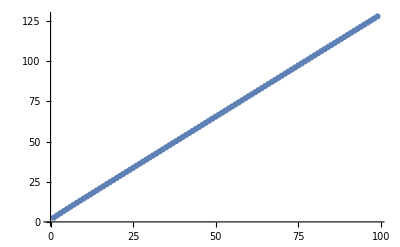

```mathematica
ListPlot[Table[cond[s[n]],{n,2,100}]]
```

```mathematica
MatrixForm[Transpose[s[4]].s[4]]
MatrixForm[Inverse[Transpose[s[4]].s[4]]]
{e1,v1}=Eigensystem[Transpose[s[4]].s[4]];
```

(1. | 1. | 1. | 1.
1. | 2. | 2. | 2.
1. | 2. | 3. | 3.
1. | 2. | 3. | 4.)

(2. | -1. | 0. | 0.
-1. | 2. | -1. | 0.
0. | -1. | 2. | -1.
0. | 0. | -1. | 1.)

```mathematica
MatrixForm[Transpose[s[5]].s[5]]
MatrixForm[Inverse[Transpose[s[5]].s[5]]]
{e2,v2}=Eigensystem[Transpose[s[5]].s[5]];
```

(1. | 1. | 1. | 1. | 1.
1. | 2. | 2. | 2. | 2.
1. | 2. | 3. | 3. | 3.
1. | 2. | 3. | 4. | 4.
1. | 2. | 3. | 4. | 5.)

(2. | -1. | 0. | 0. | 0.
-1. | 2. | -1. | 0. | 0.
0. | -1. | 2. | -1. | 0.
0. | 0. | -1. | 2. | -1.
0. | 0. | 0. | -1. | 1.)

```mathematica
e1
```

{8.29086,1.,0.426022,0.283119}

```mathematica
e2
```

{12.3435,1.44869,0.582964,0.353253,0.271554}

```mathematica
MatrixForm[Inverse[s[4]]]
```

(1. | -1. | 0. | 0.
0. | 1. | -1. | 0.
0. | 0. | 1. | -1.
0. | 0. | 0. | 1.)

```mathematica
l={{3.,-1,-1,-1},{0,2,-1,-1},{0,0,1,-1},{0,0,0,0}};
x=Eigenvectors[l]
y=Eigenvectors[Transpose[l]]
```

{{1.,0.,0.,0.},{0.707107,0.707107,0.,0.},{0.57735,0.57735,0.57735,0.},{0.5,0.5,0.5,0.5}}

{{0.707107,-0.707107,0.,0.},{0.,0.707107,-0.707107,0.},{0.,0.,0.707107,-0.707107},{0.,0.,0.,1.}}

```mathematica
Table[1/Abs[x[[i]].y[[i]]],{i,1,4}]
```

{1.41421,2.,2.44949,2.}